Tutorial: Function Basics
https://reference.wolfram.com/language/ref/Plot.html?q=Plot
https://www.wolfram.com/language/fast-introduction-for-math-students/en/differential-equations/

```mathematica
x=2
```

2

```mathematica
x+2
```

4

```mathematica
4
```

4

```mathematica
clear[x]
```

clear[2]

```mathematica
f[y_]:=1+2y
```

```mathematica
f[2]
```

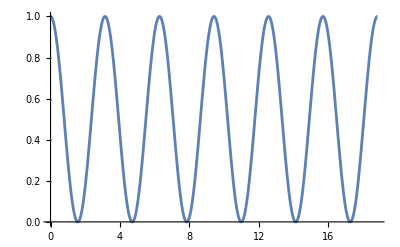

```mathematica
Plot[Sin[x]^2+Cos[2x],{x,0,6 Pi}]
```

```mathematica
Plot[{Sin[x],Sin[2 x],Sin[3 x]},{x,0,2 Pi},PlotLegends->"Expressions"]
```

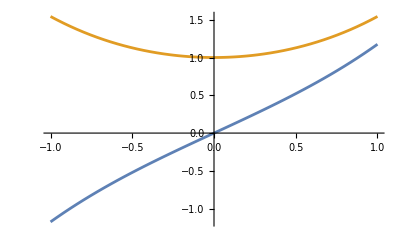

```mathematica
Plot[{Sinh[x],Cosh[x],Tanh{x}},{x,-1,+1}]
```

Define your own functions with the construction f[x_] :=

```mathematica
f[x_]:=1+2 x^2
```

```mathematica
f[5]
```

```mathematica
11
```

Derivative

```mathematica
D[f[x],x]
```

4 x

```mathematica
f[x_]:=x^2+2 x+1;
f'[x]
```

2+2 x

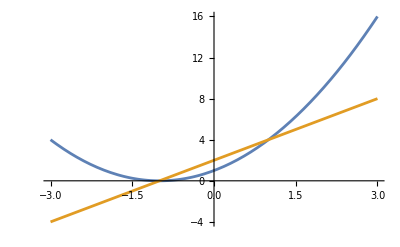

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

```mathematica
product rule formula
```

```mathematica
Entity["FamousMathProblem","ProductRule"][EntityProperty["FamousMathProblem","AssociatedEquations"]]formula product rule
```

{formula product rule d/dx(f(x) g(x)) == f(x) g'(x) + g(x) f'(x)}

```mathematica
D[(formula product rule), product]
```

formula rule

```mathematica
D[(formula rule), formula]
```

rule

```mathematica
Integrate[8 x^4,x]
```

(8 x^5)/5

Or type ESCinttESC for a fillable mathematical expression:

(For more information on fillable expressions, see Mathematical Typesetting.)

```mathematica
∫8 x^4 ⅆx
```

For definite integrals, type ESCdinttESC and specify upper and lower limits:

(8 x^5)/5

```mathematica
∫_0^π Sin[x]ⅆx
```

D works for partial derivatives—just specify which variable (s) to differentiate : Or use the ∂ symbol:

(Type ESCpdESC for ∂ and CTRL+- for subscript.)

```mathematica
D[x^3 z + 2 y^2 x + y z^3, y, z]
```

3 z^2

2

```mathematica
D[(x^2-2x y+x y z), x,y]
```

Multiple integrals use the same notation as single integrals:

(Type ESCintESC for ∫ and ESCddESC for ⅆ.)

```mathematica
∫∫∫(x^2+y^2+z^2) ⅆy ⅆx ⅆz
```

1/3 x^3 y z+1/3 x y^3 z+1/3 x y z^3

```mathematica
∫_-1^1 ∫_-2^x (x Sin[y^2]+y Cos[x^2])ⅆyⅆx
```

In the Wolfram Language, n-dimensional vectors are represented by lists of length n.

Calculate the dot product of two vectors: Type ESCcrossESC for the cross product symbol: Find the projection of a vector onto the x axis Find the angle between two vectors:

```mathematica
{1,2,3}.{a,b,c}
```

a+2 b+3 c

```mathematica
{1,2,c}×{a,b,c}
Norm[{1,1,1}]
Projection[{8,6,7},{1,0,0}]
VectorAngle[{1,0},{0,1}]
```

{2 c-b c,-c+a c,-2 a+b}

√3

{8,0,0}

π/2

Calculate the gradient of a vector:

(For the ∇ symbol, use ESCgradESC.) Compute the divergence or curl of a vector field:

```mathematica
∇_{x,y} {x^2+y,x+y^2}
```

{{2 x,1},{1,2 y}}

```mathematica
Div[{f[x,y,z],g[x,y,z],h[x,y,z]},{x,y,z}]
```

h^(0,0,1)[x,y,z]+g^(0,1,0)[x,y,z]+f^(1,0,0)[x,y,z]

The Wolfram Language has 2D and 3D functions suitable for visualizing vector fields:

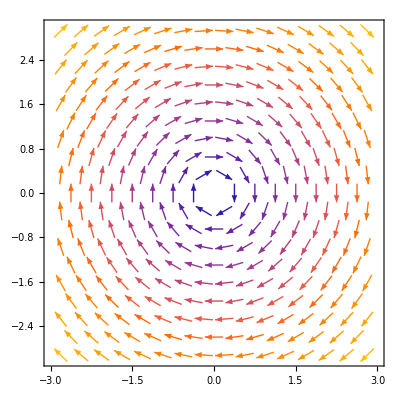

```mathematica
VectorPlot[{y, -x}, {x, -3, 3}, {y, -3, 3}]
```

```mathematica
VectorPlot3D[{y, -x, z}, {x, -3, 3}, {y, -3, 3}, {z, -3, 3}]
```

-Graphics3D-

```mathematica
SliceVectorPlot3D[{y,-x,z},"CenterPlanes",{x,-2,2},{y,-2,2},{z,-2,2}]
```

-Graphics3D-

Differential Equations
The Wolfram Language can find solutions to ordinary, partial and delay differential equations (ODEs, PDEs and DDEs).

DSolveValue takes a differential equation and returns the general solution:

(C[1] stands for a constant of integration.)

```mathematica
sol = DSolveValue[y'[x] + y[x] == x, y[x], x]
```

-1+x+ⅇ^-x C[1]

```mathematica
sol /. C[1] -> 1
```

-1+ⅇ^-x+x

```mathematica
DSolveValue[{y'[x] + y[x] == x, y[0] == -1}, y[x], x]
```

-1+x

NDSolveValue finds numerical solutions:

```mathematica
NDSolveValue[{y'[x] == Sin[x^2], y[0] == 0}, y[x], {x, -5, 5}]
```

InterpolatingFunction[…][x]

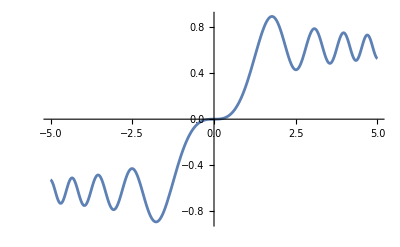

```mathematica
Plot[%, {x, -5, 5}]
```

vanderpol https://en.wikipedia.org/wiki/Van_der_Pol_oscillator

```mathematica
μ=0.5
```

0.5

```mathematica
xsol=NDSolveValue[{y''[t]- μ *(1-y[t]^2)* y'[t]+y[t]==0, y[0]==0, y'[0]==0}, y, {t, 0, 10}]
```

InterpolatingFunction[…]

```mathematica
ysol = NDSolveValue[{y''[t] -μ* y[t] == 0, y[0] == 1, 
   y'[0] == 0}, y, {t, 0, 30}]
```

InterpolatingFunction[…]

```mathematica
Plot[%, {t, 0, 30}]
```

-Graphics-

NDSolveValue::deqn: Equation or list of equations expected instead of 0 in the first argument {x[t]-0.5 (1-x[«1»]^2) x'[t]+x''[t]==0,x[0]==0,0}.

NDSolveValue[{x[t]-0.5 (1-x[t]^2) x'[t]+x''[t]==0,x[0]==0,0},x[t],{t,0,10}]

```mathematica
Plot[%, {x, 0, 10}]
```

-Graphics-

To solve systems of differential equations, include all equations and conditions in a list:

(Note that the line breaks have no effect.)

```mathematica
{xsol, ysol} = NDSolveValue[
  {x'[t] == -y[t] - x[t]^2,
   y'[t] == 2 x[t] - y[t]^3,
   x[0] == y[0] == 1},
  {x, y}, {t, 20}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

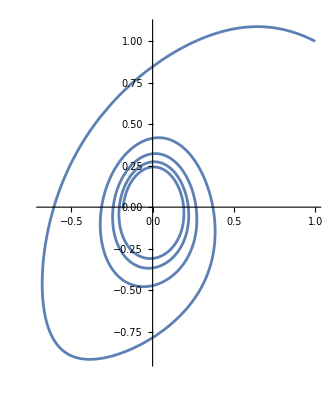

```mathematica
ParametricPlot[{xsol[t], ysol[t]}, {t, 0, 20}]
```

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
Needs["FunctionApproximations`"];
```

```mathematica
https://reference.wolfram.com/language/tutorial/NDSolveStiffnessTest.html#719449362
https://reference.wolfram.com/language/tutorial/NDSolveStiffnessTest.html#719449362Nonehttps://reference.wolfram.com/language/tutorial/NDSolveStiffnessTest.html#719449362HyperlinkActionRecycledHyperlinkActive

system=GetNDSolveProblem["VanderPol"];
solns=NDSolve[system,{T,0,10},Method->"Extrapolation"];
```

NDSolve::ndstf: At T == 0.0223269, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

```mathematica
sols=NDSolve[system,{T,0,10},Method->{"StiffnessSwitching","NonstiffTest"->False}];
```

```mathematica
Plot[Evaluate[Part[sols,1,All,2]],{T,0,10},PlotStyle->{{Red},{Blue}},Axes->False,Frame->True]
```

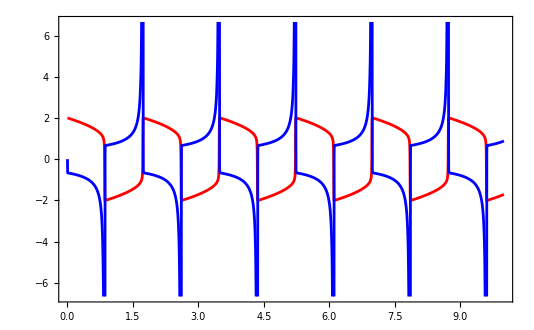

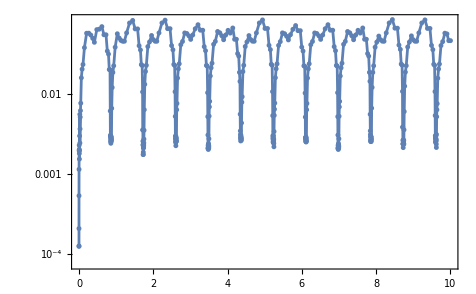

```mathematica
StepDataPlot[sols]
```

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0];
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/. x->a;
weights[n_,x_]:=2/((1-x^2) legendreprime[n,x]^2);

(*how many terms should be generated*)
h=64;

(*what numerical precision is desired?*)
precision=256;

str=OpenWrite["lgvalues.txt"];
Write[str,"abcissae"];
Do[Write[str];Write[str,n];Write[str];
nlist=symboliclegendre[n,x];
xnlist=x/. nlist;
Do[Write[str,N[Part[xnlist,i],precision]],{i,Length[xnlist]}];,{n,2,h}];
Write[str,"weights"];
Do[Write[str];Write[str,n];Write[str];
slist:=symboliclegendre[n,x];
xslist=x/. slist;
Do[Write[str,N[weights[n,Part[xslist,i]],precision]],{i,Length[xslist]}];,{n,2,h}];
Close[str];
```

```mathematica
pars=<|"MassDensity"->1.2,"SpecificHeatCapacity"->1006.14,"ThermalConductivity"->0.026|>;
```

```mathematica
pars["MassDensity"]
```

1.2

```mathematica
mypars = <|"test1"->1.3,"test2"->2.6|>
```

<|test1→1.3,test2→2.6|>

```mathematica
mypars["test1"]
```

1.3

```mathematica
il={1,2,3,4,5,6,7}
A={1,2,2,1,2,2,1}
Length[il]
Length[A]
```

{1,2,3,4,5,6,7}

{1,2,2,1,2,2,1}

7

7

```mathematica
f[x_]:=Sum[A[[i]]*Cos[x*il[[i]]*Pi],{i,1,Length[il]}]
N[f[1.25]]
```

0.414214

```mathematica
N(1.Cos[1.1.π]+1.Cos[1.4.π]+2.Cos[1.2.π]+2.Cos[1.3.π])
```

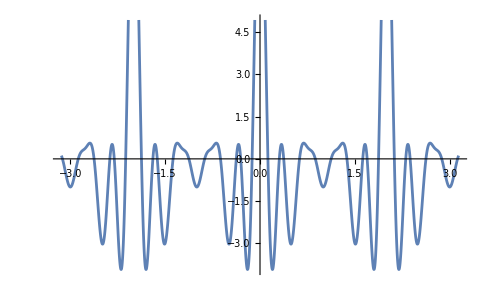

```mathematica
Plot[f[x1],{x1,-Pi,Pi}]
```

```mathematica
Show[%50,Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

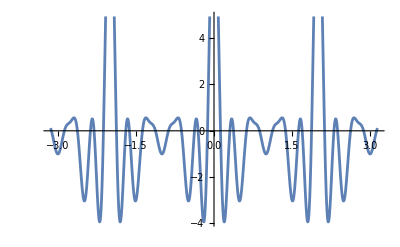

-Graphics-

```mathematica
g[x_]:=x^3-1.8*x^2+1.2*Sin[x]
ND[y_]:=g[y]/Derivative[g[y],y]
N[g[1]]
```

0.209765

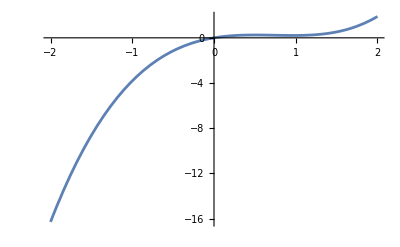

```mathematica
Plot[g[x1],{x1,-2,2}]
```

```mathematica
NE=50
x=-1.5
Do[x=x-ND[x],{i,1,NE}]
```

50

-1.5

```mathematica
g[x]/D[g[x],x]
```

D::ivar: -1.5 is not a valid variable.

```mathematica
-8.621993983924865/D[(-8.621993983924865), -1.5]
```

D::ivar: -1.5 is not a valid variable.

-8.62199/(∂_-1.5 (-8.62199))

```mathematica
Derivative[g[y],y]
```

```mathematica
Derivative[-1.8 y^2+y^3+1.2 Sin[y],y]
```

Derivative[-1.8 y^2+y^3+1.2 Sin[y],y]

```mathematica
x=-1.5
N[x-ND[x]]
```

-1.5

-1.5+8.62199/Derivative[-8.62199,-1.5]

```mathematica
N[%]
```

-1.5+8.62199/Derivative[-8.62199,-1.5]